## Gaussian beams

#### Beam spot along propagation

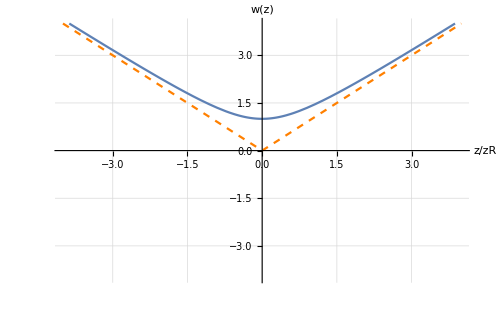

```mathematica
Show[Plot[w[1,z,1],{z,-4,4},PlotRange->{{0-4,4},{-4,4}},AxesLabel->{"z/zR","w(z)"},GridLines->Automatic,LabelStyle->Directive[Bold, Medium],AxesStyle->Directive[Darker@Gray, 12]],Plot[Abs[z],{z,-4,4},PlotStyle->Directive[{Orange,Dashed}]],ImageSize->500]
```

#### Beam’s curvature along propagation

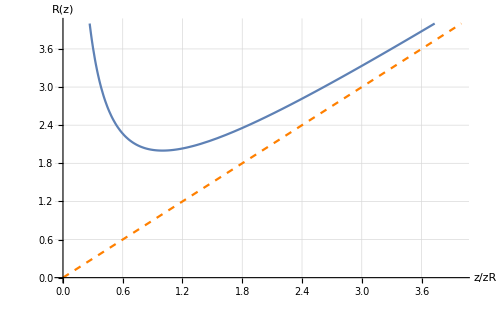

```mathematica
Show[Plot[R[z,1],{z,0,4},PlotRange->{{0,4},{0,4}},AxesLabel->{"z/zR","R(z)"},GridLines->Automatic,LabelStyle->Directive[Bold, Medium],AxesStyle->Directive[Darker@Gray, 12]],Plot[z,{z,0,4},PlotStyle->Directive[{Orange,Dashed}]],ImageSize->500]
```

#### Gouy Phase along propagation

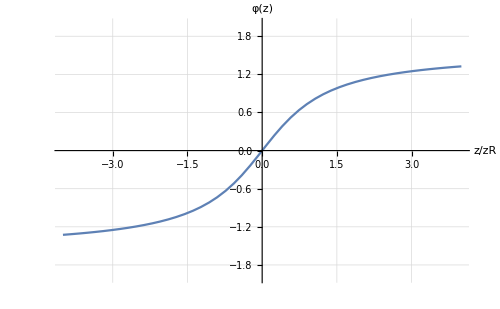

```mathematica
Show[Plot[φ[z,1],{z,-4,4},PlotRange->{{-4,4},{-2,2}},AxesLabel->{"z/zR","φ(z)"},GridLines->Automatic,LabelStyle->Directive[Bold, Medium],AxesStyle->Directive[Darker@Gray, 12]],ImageSize->500]
```

#### Intensity and phase of a Gaussian beam at z=0

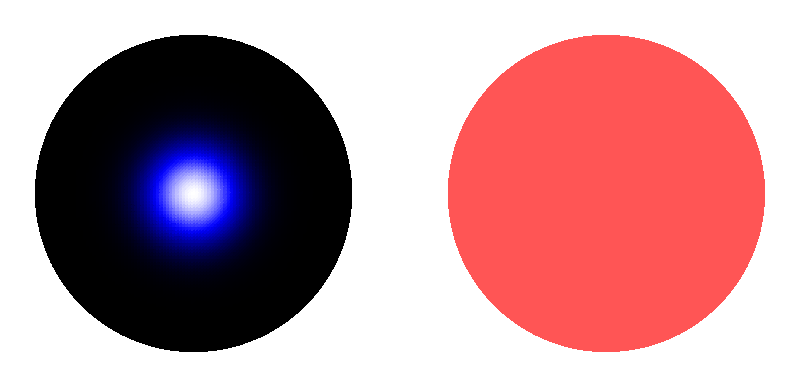

```mathematica
GraphicsRow[{Int[Gaussian[0.8]],Ph[Gaussian[0.8]]}]
```

### Higher-orders modes

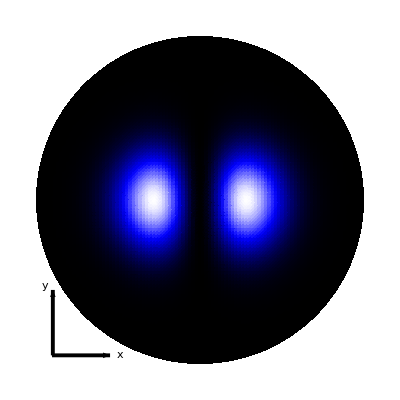

```mathematica
Show[Int[HG[1,0,0.8]],Graphics[{{Black,Thickness[0.007],Arrowheads[0.05],Arrow[{{-1.8,-1.9},{-1.8,-1.1}}]},{Black,Thickness[0.007],Arrowheads[0.05],Arrow[{{-1.81,-1.9},{-1.1,-1.9}}]}}],Graphics[{{Inset[Style["y",Black],{-1.9,-1.05},BaseStyle->Directive[Large,Italic]]},{Inset[Style["x",Black],{-.98,-1.9},BaseStyle->Directive[Large,Italic]]}}],PlotRange->All]
```

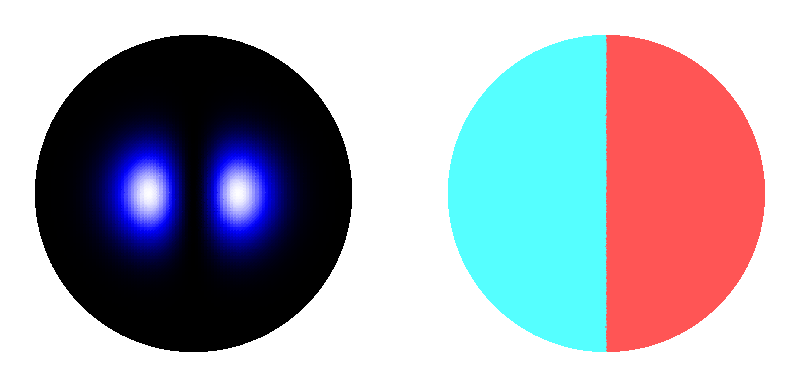

```mathematica
GraphicsRow[{Int[HG[1,0,0.8]],Ph[HG[1,0,0.8]]}]
```

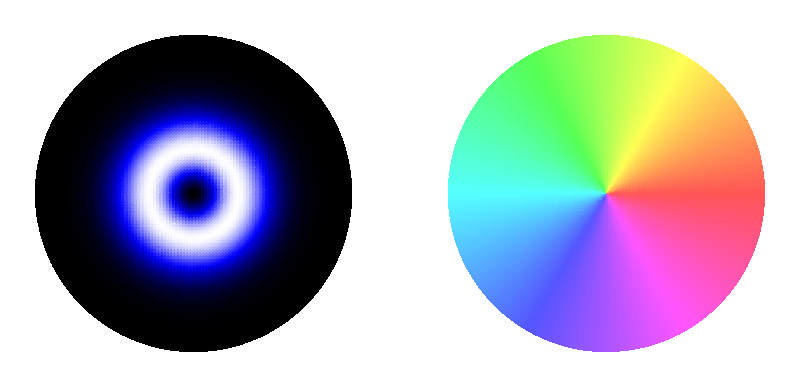

```mathematica
GraphicsRow[{Int[LG[1,0,0.8]],Ph[LG[1,0,0.8]]}]
```

## Functions

```mathematica
SetDirectory@NotebookDirectory[];
```

### Gaussian Beam parameters

```mathematica
(*Curvature of the wavefunction*)
R[z_,zR_]:=z(1+zR^2/z^2); 

(*Beam spot / waist parameter*)
w[w0_,z_,zR_]:=w0 Sqrt[1+z^2/zR^2]
(*Gouy Phase*)
φ[z_,zR_]:=ArcTan[zR,z]

zR[w0_,λ_]:=(π w0^2)/λ;
```

### Paraxial beams at z=0

```mathematica
(* Simple Gaussian Beam *)
Gaussian[w0_]:=(ⅇ^(-x^2/w0^2-y^2/w0^2) √(2/π))/w0; 

(*Laguerre-Gaussian Mode*)
LG[l_,P_:0,w0_:1]:=Sqrt[(2 Factorial[P])/(π Factorial[P+Abs[l]])] 1/w0((Sqrt[x^2+y^2]√2)/w0)^Abs[l] LaguerreL[P,Abs[l],(2(x^2+y^2))/w0^2]Exp[(-(x^2+y^2))/w0^2]Exp[ⅈ l ArcTan[x,y]]; 

(*Hermite-Gaussian Mode*)
HG[n_,l_,w0_:1]:=((2/π)^(1/4)Sqrt[1/(2^n Factorial[n])])/Sqrt[w0] HermiteH[n,(Sqrt[2]x)/w0]Exp[-x^2/w0^2]((2/π)^(1/4)Sqrt[1/(2^l Factorial[l])])/Sqrt[w0] HermiteH[l,(Sqrt[2]y)/w0]Exp[-y^2/w0^2];
```

#### Paraxial beams at z!=0

```mathematica
(*Laguerre-Gaussian Mode*)
LGz[l_,P_,w0_,λ_]:=Module[{zr,A,B},
zr=zR[w0,λ]; 
A=Sqrt[(2 Factorial[P])/(π Factorial[P+Abs[l]])] 1/Sqrt[w[w0,z,zr]]((Sqrt[x^2+y^2]√2)/w[w0,z,zR[w0,λ]])^Abs[l] Exp[(-(x^2+y^2))/w[w0,z,zr]^2]LaguerreL[P,Abs[l],(2(x^2+y^2))/w[w0,z,zr]^2]Exp[(-ⅈ 2 π)/λ  (x^2+y^2)/(2 R[z,zr])]Exp[ⅈ l ArcTan[x,y]]Exp[-ⅈ(2 P + Abs[l]+1)φ[z,zr]];
Return[A]]; 


(*Hermite-Gaussian Mode*)
HGz[n_,l_,w0_,λ_]:=Module[{zr,A,B},
zr=zR[w0,λ];
A=(2/π)^(1/4)Sqrt[1/(2^n Factorial[n])](2/π)^(1/4)Sqrt[1/(2^l Factorial[l])] 1/w[w0,z,zr] HermiteH[n,(Sqrt[2]x)/w[w0,z,zr]]HermiteH[l,(Sqrt[2]y)/w[w0,z,zr]]Exp[-x^2/w[w0,z,zr]^2]Exp[-y^2/w[w0,z,zr]^2]Exp[(-ⅈ 2 π)/λ  (x^2+y^2)/(2 R[z,zr])]
Exp[-ⅈ(n+ l+1)φ[z,zr]]; 
Return[A]]
```

### Non diffracting beams

### Tools

```mathematica
(*Simple Intensity of the beam*)
Int[ψ_,NN_:100]:=DensityPlot[Abs[ψ]^2,{x,-2,2},{y,-2,2},PlotPoints->NN,Exclusions->None,RegionFunction->Function[{x,y,f},x^2+y^2<4],ColorFunction->(Blend[{Black,Blue,White},#]&),Axes->None,Frame->False,PlotRange->All]; 
(*Simple Phase of the beam*)
Ph[ψ_,NN_:100]:=DensityPlot[Arg[ψ],{x,-2,2},{y,-2,2},ColorFunction->(Lighter@Hue[Rescale[#,{0,2π},{0,1}]]&),ColorFunctionScaling->False,PlotPoints->NN,Exclusions->None,RegionFunction->Function[{x,y,f},x^2+y^2<4],Axes->None,Frame->False];
```